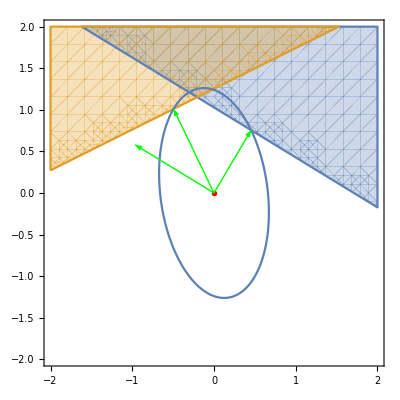

```mathematica
{a1,a2}=RandomReal[{0,1},2];
{d1,d2}=RandomReal[{-1,1},{2,2}];
{p1,p2}=Map[Normalize,{d1,d2}];
proj=Normalize[p2-(p2.p1)*p1];
{α1,α2}= {a1/Norm[d1],a2/Norm[d2]};
Show[
RegionPlot[ {a1+d1.{x,y}<0,a2+d2.{x,y}<0},{x,-2,2},{y,-2,2}],
ParametricPlot[{α1 p1 Cos[θ] + α2 p2 Sin[θ]},{θ,0, 2π}],
Epilog->{
{Red, PointSize[0.01],Point[{0,0}]},
{Green,Arrow[{{0,0}, -p1 *α1}],Arrow[{{0,0}, -p2*α2}],Arrow[{{0,0}, -α2 proj}]}
}]
```

We want to automate this orthogonalization process

```mathematica
?Disk
```

## Break